```mathematica
(*Optional: sets precision. Doesn't help though*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`150."&);

(*Checking precision*)
3/1.5+Pi/7
Precision[%]
```

2.4487989505128276054946633404685004120281670570535865458535635131868309151837441426611478321917310097117354409304689009495848349442215117473893370583

150.088

```mathematica
assum={MD2>0,MD1>0,MD2>MD1,MZp>0,Δ>0,MZ>0};
```

```mathematica
(*Sam's analytical expression for the decay rate*)
```

```mathematica
Γdec[vMD1_,vMD2_,vMZp_,vttheta_,vepsilon_,vaX_]:=(1/(7374714 MD2^3 π)5 aX epsilon^2 ttheta^2 (-(-MD1^2+MD2^2) (1000 MZ^2+80 (25 MD1^2-75 MD1 MD2+25 MD2^2-16 MZ^2-50 MZp^2)-(101 MZ^2 (-MD1^4-MD2^4+6 MD1 MD2 MZ^2-MD2^2 MZ^2+2 MZ^4+MD1^2 (2 MD2^2-MZ^2)))/((MZ^2-MZp^2)^2)+((961 MZ^4-1860 MZ^2 MZp^2+1000 MZp^4) (MD1^4+MD2^4-6 MD1 MD2 MZp^2+MD2^2 MZp^2-2 MZp^4+MD1^2 (-2 MD2^2+MZp^2)))/((-MZ^2 MZp+MZp^3)^2))-2 (3000 MD1^3 MD2-241 MZ^4-280 MZ^2 MZp^2-3000 MZp^4+60 MD1 MD2 (50 MD2^2-7 MZ^2-100 MZp^2)+30 MD1^2 (7 MZ^2+100 MZp^2)+30 MD2^2 (7 MZ^2+100 MZp^2)) Log[-2 MD1^2]+2 (3000 MD1^3 MD2-241 MZ^4-280 MZ^2 MZp^2-3000 MZp^4+60 MD1 MD2 (50 MD2^2-7 MZ^2-100 MZp^2)+30 MD1^2 (7 MZ^2+100 MZp^2)+30 MD2^2 (7 MZ^2+100 MZp^2)) Log[-2 MD1 MD2]+(2 MZ^2 (-MD1^2+2 MD1 MD2-MD2^2+MZ^2) (241 MZ^8-443 MZ^6 MZp^2-MD1^6 (31 MZ^2+70 MZp^2)-2 MD1^5 MD2 (31 MZ^2+70 MZp^2)+MD1^4 MD2^2 (31 MZ^2+70 MZp^2)-MD2^6 (31 MZ^2+70 MZp^2)+MD2^2 (-210 MZ^6+513 MZ^4 MZp^2)+MD1^3 MD2 (-179 MZ^4+583 MZ^2 MZp^2+4 MD2^2 (31 MZ^2+70 MZp^2))-MD1 MD2 (62 MZ^6+140 MZ^4 MZp^2+2 MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (179 MZ^4-583 MZ^2 MZp^2))+MD1^2 (-210 MZ^6+513 MZ^4 MZp^2+MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (-358 MZ^4+1166 MZ^2 MZp^2))) Log[-MZ^2])/(√(MD1^4+(MD2^2-MZ^2)^2-2 MD1^2 (MD2^2+MZ^2)) (MZ^2-MZp^2)^3)-(2 MZ^2 (-MD1^2+2 MD1 MD2-MD2^2+MZ^2) (241 MZ^8-443 MZ^6 MZp^2-MD1^6 (31 MZ^2+70 MZp^2)-2 MD1^5 MD2 (31 MZ^2+70 MZp^2)+MD1^4 MD2^2 (31 MZ^2+70 MZp^2)-MD2^6 (31 MZ^2+70 MZp^2)+MD2^2 (-210 MZ^6+513 MZ^4 MZp^2)+MD1^3 MD2 (-179 MZ^4+583 MZ^2 MZp^2+4 MD2^2 (31 MZ^2+70 MZp^2))-MD1 MD2 (62 MZ^6+140 MZ^4 MZp^2+2 MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (179 MZ^4-583 MZ^2 MZp^2))+MD1^2 (-210 MZ^6+513 MZ^4 MZp^2+MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (-358 MZ^4+1166 MZ^2 MZp^2))) Log[(MD1-MD2)^2-MZ^2])/(√(MD1^4+(MD2^2-MZ^2)^2-2 MD1^2 (MD2^2+MZ^2)) (MZ^2-MZp^2)^3)+(2 MZ^2 (-MD1^2+2 MD1 MD2-MD2^2+MZ^2) (241 MZ^8-443 MZ^6 MZp^2-MD1^6 (31 MZ^2+70 MZp^2)-2 MD1^5 MD2 (31 MZ^2+70 MZp^2)+MD1^4 MD2^2 (31 MZ^2+70 MZp^2)-MD2^6 (31 MZ^2+70 MZp^2)+MD2^2 (-210 MZ^6+513 MZ^4 MZp^2)+MD1^3 MD2 (-179 MZ^4+583 MZ^2 MZp^2+4 MD2^2 (31 MZ^2+70 MZp^2))-MD1 MD2 (62 MZ^6+140 MZ^4 MZp^2+2 MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (179 MZ^4-583 MZ^2 MZp^2))+MD1^2 (-210 MZ^6+513 MZ^4 MZp^2+MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (-358 MZ^4+1166 MZ^2 MZp^2))) Log[2 MD1 MD2 (MD1^2-2 MD1 MD2+MD2^2-MZ^2)])/(√(MD1^4+(MD2^2-MZ^2)^2-2 MD1^2 (MD2^2+MZ^2)) (MZ^2-MZp^2)^3)-(2 MZ^2 (-MD1^2+2 MD1 MD2-MD2^2+MZ^2) (241 MZ^8-443 MZ^6 MZp^2-MD1^6 (31 MZ^2+70 MZp^2)-2 MD1^5 MD2 (31 MZ^2+70 MZp^2)+MD1^4 MD2^2 (31 MZ^2+70 MZp^2)-MD2^6 (31 MZ^2+70 MZp^2)+MD2^2 (-210 MZ^6+513 MZ^4 MZp^2)+MD1^3 MD2 (-179 MZ^4+583 MZ^2 MZp^2+4 MD2^2 (31 MZ^2+70 MZp^2))-MD1 MD2 (62 MZ^6+140 MZ^4 MZp^2+2 MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (179 MZ^4-583 MZ^2 MZp^2))+MD1^2 (-210 MZ^6+513 MZ^4 MZp^2+MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (-358 MZ^4+1166 MZ^2 MZp^2))) Log[MD1^4+MD2^4-MD2^2 MZ^2-MD1^2 (2 MD2^2+MZ^2)+(-MD1^2+MD2^2) √(MD1^4+(MD2^2-MZ^2)^2-2 MD1^2 (MD2^2+MZ^2))])/(√(MD1^4+(MD2^2-MZ^2)^2-2 MD1^2 (MD2^2+MZ^2)) (MZ^2-MZp^2)^3)+(4 (MD1^2-2 MD1 MD2+MD2^2-MZp^2) (2 MD1^5 MD2 MZ^2 (31 MZ^2+70 MZp^2)-MD1^4 MD2^2 MZ^2 (31 MZ^2+70 MZp^2)+MD1^6 (31 MZ^4+70 MZ^2 MZp^2)+MD2^6 (31 MZ^4+70 MZ^2 MZp^2)+MZp^4 (2883 MZ^6-8401 MZ^4 MZp^2+8720 MZ^2 MZp^4-3000 MZp^6)+MD2^2 (-2883 MZ^6 MZp^2+8370 MZ^4 MZp^4-8790 MZ^2 MZp^6+3000 MZp^8)-MD1^3 MD2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6+4 MD2^2 (31 MZ^4+70 MZ^2 MZp^2))-MD1^2 (2883 MZ^6 MZp^2-8370 MZ^4 MZp^4+8790 MZ^2 MZp^6-3000 MZp^8+MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+2 MD2^2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6))+MD1 MD2 (62 MZ^4 MZp^4+140 MZ^2 MZp^6+2 MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+MD2^2 (-2883 MZ^6+8339 MZ^4 MZp^2-8860 MZ^2 MZp^4+3000 MZp^6))) Log[MZp])/((-MZ^2+MZp^2)^3 √(MD1^4+(MD2^2-MZp^2)^2-2 MD1^2 (MD2^2+MZp^2)))+(2 (MD1^2-2 MD1 MD2+MD2^2-MZp^2) (2 MD1^5 MD2 MZ^2 (31 MZ^2+70 MZp^2)-MD1^4 MD2^2 MZ^2 (31 MZ^2+70 MZp^2)+MD1^6 (31 MZ^4+70 MZ^2 MZp^2)+MD2^6 (31 MZ^4+70 MZ^2 MZp^2)+MZp^4 (2883 MZ^6-8401 MZ^4 MZp^2+8720 MZ^2 MZp^4-3000 MZp^6)+MD2^2 (-2883 MZ^6 MZp^2+8370 MZ^4 MZp^4-8790 MZ^2 MZp^6+3000 MZp^8)-MD1^3 MD2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6+4 MD2^2 (31 MZ^4+70 MZ^2 MZp^2))-MD1^2 (2883 MZ^6 MZp^2-8370 MZ^4 MZp^4+8790 MZ^2 MZp^6-3000 MZp^8+MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+2 MD2^2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6))+MD1 MD2 (62 MZ^4 MZp^4+140 MZ^2 MZp^6+2 MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+MD2^2 (-2883 MZ^6+8339 MZ^4 MZp^2-8860 MZ^2 MZp^4+3000 MZp^6))) Log[2 MD1 MD2 (MD1^2-2 MD1 MD2+MD2^2-MZp^2)])/((-MZ^2+MZp^2)^3 √(MD1^4+(MD2^2-MZp^2)^2-2 MD1^2 (MD2^2+MZp^2)))-(2 (MD1^2-2 MD1 MD2+MD2^2-MZp^2) (2 MD1^5 MD2 MZ^2 (31 MZ^2+70 MZp^2)-MD1^4 MD2^2 MZ^2 (31 MZ^2+70 MZp^2)+MD1^6 (31 MZ^4+70 MZ^2 MZp^2)+MD2^6 (31 MZ^4+70 MZ^2 MZp^2)+MZp^4 (2883 MZ^6-8401 MZ^4 MZp^2+8720 MZ^2 MZp^4-3000 MZp^6)+MD2^2 (-2883 MZ^6 MZp^2+8370 MZ^4 MZp^4-8790 MZ^2 MZp^6+3000 MZp^8)-MD1^3 MD2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6+4 MD2^2 (31 MZ^4+70 MZ^2 MZp^2))-MD1^2 (2883 MZ^6 MZp^2-8370 MZ^4 MZp^4+8790 MZ^2 MZp^6-3000 MZp^8+MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+2 MD2^2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6))+MD1 MD2 (62 MZ^4 MZp^4+140 MZ^2 MZp^6+2 MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+MD2^2 (-2883 MZ^6+8339 MZ^4 MZp^2-8860 MZ^2 MZp^4+3000 MZp^6))) Log[-(MD1-MD2)^2+MZp^2])/((-MZ^2+MZp^2)^3 √(MD1^4+(MD2^2-MZp^2)^2-2 MD1^2 (MD2^2+MZp^2)))-(2 (MD1^2-2 MD1 MD2+MD2^2-MZp^2) (2 MD1^5 MD2 MZ^2 (31 MZ^2+70 MZp^2)-MD1^4 MD2^2 MZ^2 (31 MZ^2+70 MZp^2)+MD1^6 (31 MZ^4+70 MZ^2 MZp^2)+MD2^6 (31 MZ^4+70 MZ^2 MZp^2)+MZp^4 (2883 MZ^6-8401 MZ^4 MZp^2+8720 MZ^2 MZp^4-3000 MZp^6)+MD2^2 (-2883 MZ^6 MZp^2+8370 MZ^4 MZp^4-8790 MZ^2 MZp^6+3000 MZp^8)-MD1^3 MD2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6+4 MD2^2 (31 MZ^4+70 MZ^2 MZp^2))-MD1^2 (2883 MZ^6 MZp^2-8370 MZ^4 MZp^4+8790 MZ^2 MZp^6-3000 MZp^8+MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+2 MD2^2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6))+MD1 MD2 (62 MZ^4 MZp^4+140 MZ^2 MZp^6+2 MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+MD2^2 (-2883 MZ^6+8339 MZ^4 MZp^2-8860 MZ^2 MZp^4+3000 MZp^6))) Log[MD1^4+MD2^4-MD2^2 MZp^2-MD1^2 (2 MD2^2+MZp^2)+(-MD1^2+MD2^2) √(MD1^4+(MD2^2-MZp^2)^2-2 MD1^2 (MD2^2+MZp^2))])/((-MZ^2+MZp^2)^3 √(MD1^4+(MD2^2-MZp^2)^2-2 MD1^2 (MD2^2+MZp^2)))))/.{MD1-> vMD1,MD2-> vMD2,MZp-> vMZp,ttheta-> vttheta,epsilon->  vepsilon,aX-> vaX}
```

```mathematica
Γsimple[vMD1_,vMD2_,vMZp_,vttheta_,vepsilon_,vaX_]:=(1/(7374714 MD2^3 π) 5 aX epsilon^2 ttheta^2 ((MD1^2-MD2^2) (1000 MZ^2+80 (25 MD1^2-75 MD1 MD2+25 MD2^2-16 MZ^2-50 MZp^2)-(101 MZ^2 (-MD1^4-MD2^4+6 MD1 MD2 MZ^2-MD2^2 MZ^2+2 MZ^4+MD1^2 (2 MD2^2-MZ^2)))/(MZ^2-MZp^2)^2+((961 MZ^4-1860 MZ^2 MZp^2+1000 MZp^4) (MD1^4+MD2^4-6 MD1 MD2 MZp^2+MD2^2 MZp^2-2 MZp^4+MD1^2 (-2 MD2^2+MZp^2)))/(-MZ^2 MZp+MZp^3)^2)-2 (3000 MD1^3 MD2-241 MZ^4-280 MZ^2 MZp^2-3000 MZp^4+60 MD1 MD2 (50 MD2^2-7 MZ^2-100 MZp^2)+30 MD1^2 (7 MZ^2+100 MZp^2)+30 MD2^2 (7 MZ^2+100 MZp^2)) Log[MD1/MD2]-(2 MZ^2 (-MD1^2+2 MD1 MD2-MD2^2+MZ^2) (241 MZ^8-443 MZ^6 MZp^2-MD1^6 (31 MZ^2+70 MZp^2)-2 MD1^5 MD2 (31 MZ^2+70 MZp^2)+MD1^4 MD2^2 (31 MZ^2+70 MZp^2)-MD2^6 (31 MZ^2+70 MZp^2)+MD2^2 (-210 MZ^6+513 MZ^4 MZp^2)+MD1^3 MD2 (-179 MZ^4+583 MZ^2 MZp^2+4 MD2^2 (31 MZ^2+70 MZp^2))-MD1 MD2 (62 MZ^6+140 MZ^4 MZp^2+2 MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (179 MZ^4-583 MZ^2 MZp^2))+MD1^2 (-210 MZ^6+513 MZ^4 MZp^2+MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (-358 MZ^4+1166 MZ^2 MZp^2))) Log[-((MD1^4+MD2^2 (MD2^2-MZ^2+Sqrt[MD1^4+(MD2^2-MZ^2)^2-2 MD1^2 (MD2^2+MZ^2)])-MD1^2 (2 MD2^2+MZ^2+Sqrt[MD1^4+(MD2^2-MZ^2)^2-2 MD1^2 (MD2^2+MZ^2)]))/(2 MD1 MD2 MZ^2))])/(Sqrt[MD1^4+(MD2^2-MZ^2)^2-2 MD1^2 (MD2^2+MZ^2)] (MZ^2-MZp^2)^3)-(2 (MD1^2-2 MD1 MD2+MD2^2-MZp^2) (2 MD1^5 MD2 MZ^2 (31 MZ^2+70 MZp^2)-MD1^4 MD2^2 MZ^2 (31 MZ^2+70 MZp^2)+MD1^6 (31 MZ^4+70 MZ^2 MZp^2)+MD2^6 (31 MZ^4+70 MZ^2 MZp^2)+MZp^4 (2883 MZ^6-8401 MZ^4 MZp^2+8720 MZ^2 MZp^4-3000 MZp^6)+MD2^2 (-2883 MZ^6 MZp^2+8370 MZ^4 MZp^4-8790 MZ^2 MZp^6+3000 MZp^8)-MD1^3 MD2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6+4 MD2^2 (31 MZ^4+70 MZ^2 MZp^2))-MD1^2 (2883 MZ^6 MZp^2-8370 MZ^4 MZp^4+8790 MZ^2 MZp^6-3000 MZp^8+MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+2 MD2^2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6))+MD1 MD2 (62 MZ^4 MZp^4+140 MZ^2 MZp^6+2 MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+MD2^2 (-2883 MZ^6+8339 MZ^4 MZp^2-8860 MZ^2 MZp^4+3000 MZp^6))) Log[-((MD1^4+MD2^2 (MD2^2-MZp^2+Sqrt[MD1^4+(MD2^2-MZp^2)^2-2 MD1^2 (MD2^2+MZp^2)])-MD1^2 (2 MD2^2+MZp^2+Sqrt[MD1^4+(MD2^2-MZp^2)^2-2 MD1^2 (MD2^2+MZp^2)]))/(2 MD1 MD2 MZp^2))])/((-MZ^2+MZp^2)^3 Sqrt[MD1^4+(MD2^2-MZp^2)^2-2 MD1^2 (MD2^2+MZp^2)])))/.{MD1-> vMD1,MD2-> vMD2,MZp-> vMZp,ttheta-> vttheta,epsilon->  vepsilon,aX-> vaX};
```

```mathematica
Export["decay_rate.dat",FortranForm[Γsimple[MD1,MD2,MZp,ttheta,epsilon,aX]]];
```

```mathematica
(*Γ multiplied by 1. which makes it obey our precision equirements*)
```

```mathematica
ΓdecNum[vMD1_,vMD2_,vMZp_,vttheta_,vepsilon_,vaX_]:=1. (1/(7374714 MD2^3 π)5aX epsilon^2 ttheta^2 (-(-MD1^2+MD2^2) (1000 MZ^2+80 (25 MD1^2-75 MD1 MD2+25 MD2^2-16 MZ^2-50 MZp^2)-(101 MZ^2 (-MD1^4-MD2^4+6 MD1 MD2 MZ^2-MD2^2 MZ^2+2 MZ^4+MD1^2 (2 MD2^2-MZ^2)))/((MZ^2-MZp^2)^2)+((961 MZ^4-1860 MZ^2 MZp^2+1000 MZp^4) (MD1^4+MD2^4-6 MD1 MD2 MZp^2+MD2^2 MZp^2-2 MZp^4+MD1^2 (-2 MD2^2+MZp^2)))/((-MZ^2 MZp+MZp^3)^2))-2 (3000 MD1^3 MD2-241 MZ^4-280 MZ^2 MZp^2-3000 MZp^4+60 MD1 MD2 (50 MD2^2-7 MZ^2-100 MZp^2)+30 MD1^2 (7 MZ^2+100 MZp^2)+30 MD2^2 (7 MZ^2+100 MZp^2)) Log[-2 MD1^2]+2 (3000 MD1^3 MD2-241 MZ^4-280 MZ^2 MZp^2-3000 MZp^4+60 MD1 MD2 (50 MD2^2-7 MZ^2-100 MZp^2)+30 MD1^2 (7 MZ^2+100 MZp^2)+30 MD2^2 (7 MZ^2+100 MZp^2)) Log[-2 MD1 MD2]+(2 MZ^2 (-MD1^2+2 MD1 MD2-MD2^2+MZ^2) (241 MZ^8-443 MZ^6 MZp^2-MD1^6 (31 MZ^2+70 MZp^2)-2 MD1^5 MD2 (31 MZ^2+70 MZp^2)+MD1^4 MD2^2 (31 MZ^2+70 MZp^2)-MD2^6 (31 MZ^2+70 MZp^2)+MD2^2 (-210 MZ^6+513 MZ^4 MZp^2)+MD1^3 MD2 (-179 MZ^4+583 MZ^2 MZp^2+4 MD2^2 (31 MZ^2+70 MZp^2))-MD1 MD2 (62 MZ^6+140 MZ^4 MZp^2+2 MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (179 MZ^4-583 MZ^2 MZp^2))+MD1^2 (-210 MZ^6+513 MZ^4 MZp^2+MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (-358 MZ^4+1166 MZ^2 MZp^2))) Log[-MZ^2])/(√(MD1^4+(MD2^2-MZ^2)^2-2 MD1^2 (MD2^2+MZ^2)) (MZ^2-MZp^2)^3)-(2 MZ^2 (-MD1^2+2 MD1 MD2-MD2^2+MZ^2) (241 MZ^8-443 MZ^6 MZp^2-MD1^6 (31 MZ^2+70 MZp^2)-2 MD1^5 MD2 (31 MZ^2+70 MZp^2)+MD1^4 MD2^2 (31 MZ^2+70 MZp^2)-MD2^6 (31 MZ^2+70 MZp^2)+MD2^2 (-210 MZ^6+513 MZ^4 MZp^2)+MD1^3 MD2 (-179 MZ^4+583 MZ^2 MZp^2+4 MD2^2 (31 MZ^2+70 MZp^2))-MD1 MD2 (62 MZ^6+140 MZ^4 MZp^2+2 MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (179 MZ^4-583 MZ^2 MZp^2))+MD1^2 (-210 MZ^6+513 MZ^4 MZp^2+MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (-358 MZ^4+1166 MZ^2 MZp^2))) Log[(MD1-MD2)^2-MZ^2])/(√(MD1^4+(MD2^2-MZ^2)^2-2 MD1^2 (MD2^2+MZ^2)) (MZ^2-MZp^2)^3)+(2 MZ^2 (-MD1^2+2 MD1 MD2-MD2^2+MZ^2) (241 MZ^8-443 MZ^6 MZp^2-MD1^6 (31 MZ^2+70 MZp^2)-2 MD1^5 MD2 (31 MZ^2+70 MZp^2)+MD1^4 MD2^2 (31 MZ^2+70 MZp^2)-MD2^6 (31 MZ^2+70 MZp^2)+MD2^2 (-210 MZ^6+513 MZ^4 MZp^2)+MD1^3 MD2 (-179 MZ^4+583 MZ^2 MZp^2+4 MD2^2 (31 MZ^2+70 MZp^2))-MD1 MD2 (62 MZ^6+140 MZ^4 MZp^2+2 MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (179 MZ^4-583 MZ^2 MZp^2))+MD1^2 (-210 MZ^6+513 MZ^4 MZp^2+MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (-358 MZ^4+1166 MZ^2 MZp^2))) Log[2 MD1 MD2 (MD1^2-2 MD1 MD2+MD2^2-MZ^2)])/(√(MD1^4+(MD2^2-MZ^2)^2-2 MD1^2 (MD2^2+MZ^2)) (MZ^2-MZp^2)^3)-(2 MZ^2 (-MD1^2+2 MD1 MD2-MD2^2+MZ^2) (241 MZ^8-443 MZ^6 MZp^2-MD1^6 (31 MZ^2+70 MZp^2)-2 MD1^5 MD2 (31 MZ^2+70 MZp^2)+MD1^4 MD2^2 (31 MZ^2+70 MZp^2)-MD2^6 (31 MZ^2+70 MZp^2)+MD2^2 (-210 MZ^6+513 MZ^4 MZp^2)+MD1^3 MD2 (-179 MZ^4+583 MZ^2 MZp^2+4 MD2^2 (31 MZ^2+70 MZp^2))-MD1 MD2 (62 MZ^6+140 MZ^4 MZp^2+2 MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (179 MZ^4-583 MZ^2 MZp^2))+MD1^2 (-210 MZ^6+513 MZ^4 MZp^2+MD2^4 (31 MZ^2+70 MZp^2)+MD2^2 (-358 MZ^4+1166 MZ^2 MZp^2))) Log[MD1^4+MD2^4-MD2^2 MZ^2-MD1^2 (2 MD2^2+MZ^2)+(-MD1^2+MD2^2) √(MD1^4+(MD2^2-MZ^2)^2-2 MD1^2 (MD2^2+MZ^2))])/(√(MD1^4+(MD2^2-MZ^2)^2-2 MD1^2 (MD2^2+MZ^2)) (MZ^2-MZp^2)^3)+(4 (MD1^2-2 MD1 MD2+MD2^2-MZp^2) (2 MD1^5 MD2 MZ^2 (31 MZ^2+70 MZp^2)-MD1^4 MD2^2 MZ^2 (31 MZ^2+70 MZp^2)+MD1^6 (31 MZ^4+70 MZ^2 MZp^2)+MD2^6 (31 MZ^4+70 MZ^2 MZp^2)+MZp^4 (2883 MZ^6-8401 MZ^4 MZp^2+8720 MZ^2 MZp^4-3000 MZp^6)+MD2^2 (-2883 MZ^6 MZp^2+8370 MZ^4 MZp^4-8790 MZ^2 MZp^6+3000 MZp^8)-MD1^3 MD2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6+4 MD2^2 (31 MZ^4+70 MZ^2 MZp^2))-MD1^2 (2883 MZ^6 MZp^2-8370 MZ^4 MZp^4+8790 MZ^2 MZp^6-3000 MZp^8+MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+2 MD2^2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6))+MD1 MD2 (62 MZ^4 MZp^4+140 MZ^2 MZp^6+2 MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+MD2^2 (-2883 MZ^6+8339 MZ^4 MZp^2-8860 MZ^2 MZp^4+3000 MZp^6))) Log[MZp])/((-MZ^2+MZp^2)^3 √(MD1^4+(MD2^2-MZp^2)^2-2 MD1^2 (MD2^2+MZp^2)))+(2 (MD1^2-2 MD1 MD2+MD2^2-MZp^2) (2 MD1^5 MD2 MZ^2 (31 MZ^2+70 MZp^2)-MD1^4 MD2^2 MZ^2 (31 MZ^2+70 MZp^2)+MD1^6 (31 MZ^4+70 MZ^2 MZp^2)+MD2^6 (31 MZ^4+70 MZ^2 MZp^2)+MZp^4 (2883 MZ^6-8401 MZ^4 MZp^2+8720 MZ^2 MZp^4-3000 MZp^6)+MD2^2 (-2883 MZ^6 MZp^2+8370 MZ^4 MZp^4-8790 MZ^2 MZp^6+3000 MZp^8)-MD1^3 MD2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6+4 MD2^2 (31 MZ^4+70 MZ^2 MZp^2))-MD1^2 (2883 MZ^6 MZp^2-8370 MZ^4 MZp^4+8790 MZ^2 MZp^6-3000 MZp^8+MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+2 MD2^2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6))+MD1 MD2 (62 MZ^4 MZp^4+140 MZ^2 MZp^6+2 MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+MD2^2 (-2883 MZ^6+8339 MZ^4 MZp^2-8860 MZ^2 MZp^4+3000 MZp^6))) Log[2 MD1 MD2 (MD1^2-2 MD1 MD2+MD2^2-MZp^2)])/((-MZ^2+MZp^2)^3 √(MD1^4+(MD2^2-MZp^2)^2-2 MD1^2 (MD2^2+MZp^2)))-(2 (MD1^2-2 MD1 MD2+MD2^2-MZp^2) (2 MD1^5 MD2 MZ^2 (31 MZ^2+70 MZp^2)-MD1^4 MD2^2 MZ^2 (31 MZ^2+70 MZp^2)+MD1^6 (31 MZ^4+70 MZ^2 MZp^2)+MD2^6 (31 MZ^4+70 MZ^2 MZp^2)+MZp^4 (2883 MZ^6-8401 MZ^4 MZp^2+8720 MZ^2 MZp^4-3000 MZp^6)+MD2^2 (-2883 MZ^6 MZp^2+8370 MZ^4 MZp^4-8790 MZ^2 MZp^6+3000 MZp^8)-MD1^3 MD2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6+4 MD2^2 (31 MZ^4+70 MZ^2 MZp^2))-MD1^2 (2883 MZ^6 MZp^2-8370 MZ^4 MZp^4+8790 MZ^2 MZp^6-3000 MZp^8+MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+2 MD2^2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6))+MD1 MD2 (62 MZ^4 MZp^4+140 MZ^2 MZp^6+2 MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+MD2^2 (-2883 MZ^6+8339 MZ^4 MZp^2-8860 MZ^2 MZp^4+3000 MZp^6))) Log[-(MD1-MD2)^2+MZp^2])/((-MZ^2+MZp^2)^3 √(MD1^4+(MD2^2-MZp^2)^2-2 MD1^2 (MD2^2+MZp^2)))-(2 (MD1^2-2 MD1 MD2+MD2^2-MZp^2) (2 MD1^5 MD2 MZ^2 (31 MZ^2+70 MZp^2)-MD1^4 MD2^2 MZ^2 (31 MZ^2+70 MZp^2)+MD1^6 (31 MZ^4+70 MZ^2 MZp^2)+MD2^6 (31 MZ^4+70 MZ^2 MZp^2)+MZp^4 (2883 MZ^6-8401 MZ^4 MZp^2+8720 MZ^2 MZp^4-3000 MZp^6)+MD2^2 (-2883 MZ^6 MZp^2+8370 MZ^4 MZp^4-8790 MZ^2 MZp^6+3000 MZp^8)-MD1^3 MD2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6+4 MD2^2 (31 MZ^4+70 MZ^2 MZp^2))-MD1^2 (2883 MZ^6 MZp^2-8370 MZ^4 MZp^4+8790 MZ^2 MZp^6-3000 MZp^8+MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+2 MD2^2 (2883 MZ^6-8339 MZ^4 MZp^2+8860 MZ^2 MZp^4-3000 MZp^6))+MD1 MD2 (62 MZ^4 MZp^4+140 MZ^2 MZp^6+2 MD2^4 (31 MZ^4+70 MZ^2 MZp^2)+MD2^2 (-2883 MZ^6+8339 MZ^4 MZp^2-8860 MZ^2 MZp^4+3000 MZp^6))) Log[MD1^4+MD2^4-MD2^2 MZp^2-MD1^2 (2 MD2^2+MZp^2)+(-MD1^2+MD2^2) √(MD1^4+(MD2^2-MZp^2)^2-2 MD1^2 (MD2^2+MZp^2))])/((-MZ^2+MZp^2)^3 √(MD1^4+(MD2^2-MZp^2)^2-2 MD1^2 (MD2^2+MZp^2)))))/.{MD1-> vMD1,MD2-> vMD2,MZp-> vMZp,ttheta-> vttheta,epsilon->  vepsilon,aX-> vaX}
```

```mathematica
(*Precisions of different versions of Γdec and parameters*)
```

```mathematica
Γdec[100,101,300,10^-5,10^-4,1]/.MZ-> 92000//N
Precision[%]
$MachinePrecision
```

2.81139×10^-23+0. ⅈ

MachinePrecision

15.9546

```mathematica
ΓdecNum[100,101,300,10^-5,10^-4,1]/.MZ-> 92000
Precision[%]
```

8.07243811862188666423038921943219090055398035249160586263906578248532441760701071890165112040611098733966864347642031227954292786339235918214078164002×10^-32+0. ⅈ

150.

```mathematica
ΓdecNum[100.,101.,300.,1./100000.,1./10000.,1.]/.MZ-> 92000.
Precision[%]
```

8.07243811862188666423038921943219090055398035249160586263906578248532441760701071890165112040611098733966864347642031227954×10^-32+0. ⅈ

123.694

```mathematica
(*default version*)
```

```mathematica
list=Transpose[{Range[100,110,0.2],N[Re[Γdec[100,#,300,10^-5,10^-4,1]/.MZ-> 92000],10]&/@Range[100,110,0.2]}];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ((24752632636869897459600000000000 √5 Log[300])/606335658939754471-(12376316318434948729800000000000 √5 Log[90000])/606335658939754471)/(1474942800000000000000000000000 π).

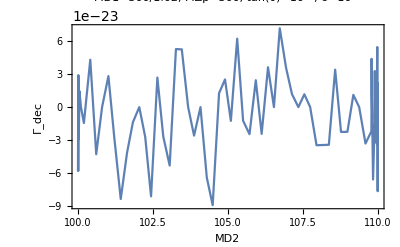

```mathematica
Plot[N[Re[Γdec[100,MD2,300,10^-5,10^-4,1]/.MZ-> 92000],10],{MD2,100,110},Frame->True,FrameLabel->{"MD2","Γ_dec"},PlotLabel->"MD1=300/1.02, MZp=300, tan(θ)=10^-5, ϵ=10^-4"]
```

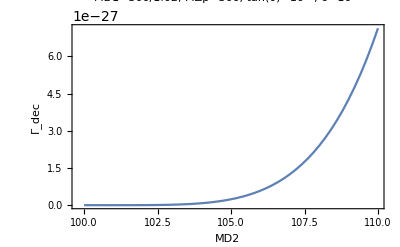

```mathematica
ListPlot[list,Frame->True,FrameLabel->{"MD2","Γ_dec"},Joined->True,PlotLabel->"MD1=300/1.02, MZp=300, tan(θ)=10^-5, ϵ=10^-4"]
```

```mathematica
(*Num. version behaves better but there are still wiggles around zero*)
```

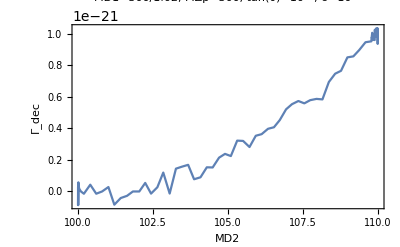

```mathematica
Plot[Re[ΓdecNum[100,101,300,10^-5,10^-4,1]/.MZ-> 92000],{MD2,100,110},Frame->True,FrameLabel->{"MD2","Γ_dec"},PlotLabel->"MD1=300/1.02, MZp=300, tan(θ)=10^-5, ϵ=10^-4"]
```

```mathematica
(*Checking dark photon limit. Looks correct. Note: if you want to check this limit yourself, you need to restart kernel and skip the precision handle*)
```

```mathematica
FullSimplify[Series[Γdec[MD1,MD2,MZp,ttheta,epsilon,aX]/.{MD1-> δm1 MZp,MD2-> δm2 MZp}/.δm2-> δm1(1+Δ),{δm1,0,5},{Δ,0,5}],assum]
```

O[Δ]^6/δm1^3+O[Δ]^6/δm1+O[Δ]^6 δm1+O[Δ]^6 δm1^3+((8 aX epsilon^2 MZp ttheta^2 Δ^5)/(3837 π)+O[Δ]^6) δm1^5+O[δm1]^6

```mathematica
(*Checking scaling: Gamma ~ [M]*)
```

```mathematica
const=10^-1;
N[ΓdecNum[const 100,const 101,const 300,10^-5,10^-4,1]/.MZ-> const 92000,5]
```

8.0724×10^-33+0. ⅈ

```mathematica
const=10;
N[ΓdecNum[const 100,const 101,const 300,10^-5,10^-4,1]/.MZ-> const 92000,5]
```

8.0724×10^-31+0. ⅈ

```mathematica
const=100;
N[ΓdecNum[const 100,const 101,const 300,10^-5,10^-4,1]/.MZ-> const 92000,5]
```

8.0724×10^-30+0. ⅈ

```mathematica
(*Rescaling variables to get decent precision*)
```

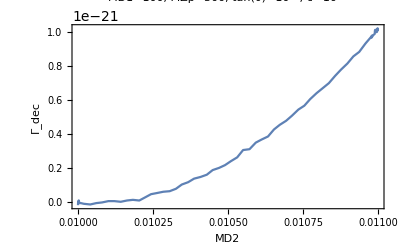

```mathematica
const=10^-4;
Plot[Re[ΓdecNum[const 100,const 101,const 300,10^-5,10^-4,1]/.MZ-> const 92000]/const,{MD2,const 100,const 110},Frame->True,FrameLabel->{"MD2","Γ_dec"},PlotLabel->"MD1=100, MZp=300, tan(θ)=10^-5, ϵ=10^-4"]
```

```mathematica
(*Checking the numbers. The first number is hard to calculate since it's a numerical zero*)
```

```mathematica
const=10^0;
N[Re[Γdec[const 100,#,const 300,10^-5,10^-4,1]/.MZ-> const 92000]/const,10]&/@Range[const 100,const 110, const 1]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ((24752632636869897459600000000000 √5 Log[300])/606335658939754471-(12376316318434948729800000000000 √5 Log[90000])/606335658939754471)/(1474942800000000000000000000000 π).

{0.,8.072438119×10^-32,2.545693746×10^-30,1.905554992×10^-29,7.917342278×10^-29,2.38284974×10^-28,5.848853632×10^-28,1.247300518×10^-27,2.39990295×10^-27,4.268876011×10^-27,7.137574875×10^-27}

```mathematica
const=10^0;
N[Re[ΓdecNum[const 100,#,const 300,10^-5,10^-4,1]/.MZ-> const 92000]/const,10]&/@Range[const 100,const 110, const 1]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (24752632636869897459600000000000 √5 Log[300])/606335658939754471-(12376316318434948729800000000000 √5 Log[90000])/606335658939754471.

{0.,8.072438119×10^-32,2.545693746×10^-30,1.905554992×10^-29,7.917342278×10^-29,2.38284974×10^-28,5.848853632×10^-28,1.247300518×10^-27,2.39990295×10^-27,4.268876011×10^-27,7.137574875×10^-27}

```mathematica
const=10^-4;
N[Re[ΓdecNum[const 100,#,const 300,10^-5,10^-4,1]/.MZ-> const 92000]/const,10]&/@Range[const 100,const 110, const 1]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(61881581592174743649 Log[100/3])/(3031678294698772355000 √5)+(61881581592174743649 Log[10000/9])/(6063356589397544710000 √5).

{0.,8.072438119×10^-32,2.545693746×10^-30,1.905554992×10^-29,7.917342278×10^-29,2.38284974×10^-28,5.848853632×10^-28,1.247300518×10^-27,2.39990295×10^-27,4.268876011×10^-27,7.137574875×10^-27}

```mathematica
Range[const 100,const 110, const 1]//N
```

{100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.}

```mathematica
(*//N*)
```

```mathematica
Re[Γdec[ 100,130, 300,10^-5,10^-4,1]/.MZ->  92000]//N
Precision[%]
$MachinePrecision
```

-1.97763×10^-23

MachinePrecision

15.9546

```mathematica
(*N[...,10]*)
```

```mathematica
N[Re[Γdec[ 100,130, 300,10^-5,10^-4,1]/.MZ->  92000],10]
Precision[%]
```

1.396276436×10^-24

10.

```mathematica
N[Re[Γsimple[ 100,130, 300,10^-5,10^-4,1]/.MZ->  92000],10]
Precision[%]
```

1.396276436×10^-24

10.

```mathematica
(*Our num. redefinition*)
```

```mathematica
Re[ΓdecNum[ 100,130, 300,10^-5,10^-4,1]/.MZ->  92000]//N
```

1.39628×10^-24

### New Sam’s version

```mathematica
ΓdecNew[vMD1_,vMD2_,vMZp_,vttheta_,vepsilon_,vaX_]:=(5*aX*epsilon^2*ttheta^2*((MD1^2-MD2^2)*(1000*MZ^2+80*(25*MD1^2-75*MD1*MD2+25*MD2^2-16*MZ^2-50*MZp^2)-(101*MZ^2*(-MD1^4-MD2^4+6*MD1*MD2*MZ^2-MD2^2*MZ^2+2*MZ^4+MD1^2*(2*MD2^2-MZ^2)))/(MZ^2-MZp^2)^2+((961*MZ^4-1860*MZ^2*MZp^2+1000*MZp^4)*(MD1^4+MD2^4-6*MD1*MD2*MZp^2+MD2^2*MZp^2-2*MZp^4+MD1^2*(-2*MD2^2+MZp^2)))/(-(MZ^2*MZp)+MZp^3)^2)-2*(3000*MD1^3*MD2-241*MZ^4-280*MZ^2*MZp^2-3000*MZp^4+60*MD1*MD2*(50*MD2^2-7*MZ^2-100*MZp^2)+30*MD1^2*(7*MZ^2+100*MZp^2)+30*MD2^2*(7*MZ^2+100*MZp^2))*Log[MD1/MD2]-(2*MZ^2*(-MD1^2+2*MD1*MD2-MD2^2+MZ^2)*(241*MZ^8-443*MZ^6*MZp^2-MD1^6*(31*MZ^2+70*MZp^2)-2*MD1^5*MD2*(31*MZ^2+70*MZp^2)+MD1^4*MD2^2*(31*MZ^2+70*MZp^2)-MD2^6*(31*MZ^2+70*MZp^2)+MD2^2*(-210*MZ^6+513*MZ^4*MZp^2)+MD1^3*MD2*(-179*MZ^4+583*MZ^2*MZp^2+4*MD2^2*(31*MZ^2+70*MZp^2))-MD1*MD2*(62*MZ^6+140*MZ^4*MZp^2+2*MD2^4*(31*MZ^2+70*MZp^2)+MD2^2*(179*MZ^4-583*MZ^2*MZp^2))+MD1^2*(-210*MZ^6+513*MZ^4*MZp^2+MD2^4*(31*MZ^2+70*MZp^2)+MD2^2*(-358*MZ^4+1166*MZ^2*MZp^2)))*Log[-(MD1^4+MD2^2*(MD2^2-MZ^2+√(MD1^4+(MD2^2-MZ^2)^2-2*MD1^2*(MD2^2+MZ^2)))-MD1^2*(2*MD2^2+MZ^2+√(MD1^4+(MD2^2-MZ^2)^2-2*MD1^2*(MD2^2+MZ^2))))/(2.*MD1*MD2*MZ^2)])/(√(MD1^4+(MD2^2-MZ^2)^2-2*MD1^2*(MD2^2+MZ^2))*(MZ^2-MZp^2)^3)-(2*(MD1^2-2*MD1*MD2+MD2^2-MZp^2)*(2*MD1^5*MD2*MZ^2*(31*MZ^2+70*MZp^2)-MD1^4*MD2^2*MZ^2*(31*MZ^2+70*MZp^2)+MD1^6*(31*MZ^4+70*MZ^2*MZp^2)+MD2^6*(31*MZ^4+70*MZ^2*MZp^2)+MZp^4*(2883*MZ^6-8401*MZ^4*MZp^2+8720*MZ^2*MZp^4-3000*MZp^6)+MD2^2*(-2883*MZ^6*MZp^2+8370*MZ^4*MZp^4-8790*MZ^2*MZp^6+3000*MZp^8)-MD1^3*MD2*(2883*MZ^6-8339*MZ^4*MZp^2+8860*MZ^2*MZp^4-3000*MZp^6+4*MD2^2*(31*MZ^4+70*MZ^2*MZp^2))-MD1^2*(2883*MZ^6*MZp^2-8370*MZ^4*MZp^4+8790*MZ^2*MZp^6-3000*MZp^8+MD2^4*(31*MZ^4+70*MZ^2*MZp^2)+2*MD2^2*(2883*MZ^6-8339*MZ^4*MZp^2+8860*MZ^2*MZp^4-3000*MZp^6))+MD1*MD2*(62*MZ^4*MZp^4+140*MZ^2*MZp^6+2*MD2^4*(31*MZ^4+70*MZ^2*MZp^2)+MD2^2*(-2883*MZ^6+8339*MZ^4*MZp^2-8860*MZ^2*MZp^4+3000*MZp^6)))*Log[-(MD1^4+MD2^2*(MD2^2-MZp^2+√(MD1^4+(MD2^2-MZp^2)^2-2*MD1^2*(MD2^2+MZp^2)))-MD1^2*(2*MD2^2+MZp^2+√(MD1^4+(MD2^2-MZp^2)^2-2*MD1^2*(MD2^2+MZp^2))))/(2.*MD1*MD2*MZp^2)])/((-MZ^2+MZp^2)^3*√(MD1^4+(MD2^2-MZp^2)^2-2*MD1^2*(MD2^2+MZp^2)))))/(7.374714 10^6*MD2^3*π)/.{MD1-> vMD1,MD2-> vMD2,MZp-> vMZp,ttheta-> vttheta,epsilon->  vepsilon,aX-> vaX}
```

```mathematica
ΓdecNew[100,120,300,10^-3,10^-4,1]/.MZ-> 92000
```

6.54789×10^-21